# Defining a Channel

i.i.d Complex Gaussian Channel ,Correlative Channel,Correlative Channel

```mathematica
(*Set the parameters*)
k=30; (*Number of users*)
P=5;  (*Transmission power in Watts*)
t=2; (*Number of antena in BS*)
Puniformal = P/t// N;
CH1 :=Table[RandomVariate[NormalDistribution[0,0.5]] +I*RandomVariate[NormalDistribution[0,0.5]],{t},{k}]
Print["Channel 1-i.i.d Complex Gaussian Channel"]
CH1//MatrixForm
sigma :=RandomVariate[UniformDistribution[{0,3}]];
mu := RandomVariate[UniformDistribution[{0,1}]];
CH2 := Table[RandomVariate[NormalDistribution[mu,sigma]] +I*RandomVariate[NormalDistribution[mu,sigma]],{t},{k}]
Print["Channel 2-Chaotic Channel"]
CH2 //MatrixForm
CH3:=ConstantArray[Table[RandomVariate[NormalDistribution[0,1]] +I*RandomVariate[NormalDistribution[0,1]],{k}],{t}];
Print["Channel 3-Correlative Channel"]
CH3 //MatrixForm
```

Channel 1-i.i.d Complex Gaussian Channel

(-0.0374159+0.522065 ⅈ | 0.167965-0.527225 ⅈ | 0.24871-0.114441 ⅈ | -0.806145+0.319998 ⅈ | 0.367712+0.416848 ⅈ | -0.0044407+0.284864 ⅈ | -0.755004-0.328397 ⅈ | -0.44072-0.0917382 ⅈ | 0.395495+0.319727 ⅈ | 0.159945+0.81186 ⅈ | 0.518345-0.437806 ⅈ | 0.188504-0.2871 ⅈ | 0.512319+0.233823 ⅈ | 0.141164-0.295087 ⅈ | 0.506745+0.520296 ⅈ | 0.624164-0.252724 ⅈ | -0.194149+0.116641 ⅈ | -0.334738+0.654867 ⅈ | -0.403413-0.452864 ⅈ | 0.40411+0.721105 ⅈ | 0.478822-0.239352 ⅈ | -0.112652+0.221823 ⅈ | 0.142-0.411386 ⅈ | 0.679979+0.393646 ⅈ | 0.487898+0.163614 ⅈ | -0.227238+0.0936829 ⅈ | -0.63094+0.545833 ⅈ | -0.0919704-0.0272433 ⅈ | 0.214433+0.0261691 ⅈ | 0.348489-0.309813 ⅈ
0.697895+0.274728 ⅈ | 0.205917-0.933668 ⅈ | -1.37137-0.255713 ⅈ | -0.230308+0.333501 ⅈ | 0.250763+0.330162 ⅈ | 0.0880918-0.576641 ⅈ | -0.0144369+0.659733 ⅈ | -0.158033+0.150727 ⅈ | -0.767364-0.126923 ⅈ | 0.509775+0.0661721 ⅈ | 0.00347006+0.555332 ⅈ | -0.107333+0.463011 ⅈ | 0.577169-0.274677 ⅈ | -0.886607-0.265673 ⅈ | -0.273682-0.400626 ⅈ | 0.251796+0.24571 ⅈ | 0.0915727+0.640803 ⅈ | 0.442389+0.470907 ⅈ | 0.230838-0.936074 ⅈ | -0.15551-0.0496195 ⅈ | 0.221366-0.00223436 ⅈ | 0.313818+1.52143 ⅈ | 0.222525+0.292216 ⅈ | 0.5136-0.201519 ⅈ | -0.350122-0.280106 ⅈ | -0.928375+0.927247 ⅈ | 0.243507+1.10828 ⅈ | -0.470036+0.0799279 ⅈ | -0.859187+0.0881866 ⅈ | 0.295146+0.0915902 ⅈ)

Channel 2-Chaotic Channel

(1.79556-1.28872 ⅈ | 0.750391+2.7809 ⅈ | 0.899973+1.54275 ⅈ | -0.687469+2.21271 ⅈ | -0.922509+0.512485 ⅈ | 1.13672+0.409591 ⅈ | -0.246498-0.341275 ⅈ | -1.30732-0.419489 ⅈ | 1.12761+0.067307 ⅈ | 1.92425+1.29174 ⅈ | -2.36642+3.19809 ⅈ | 0.341344+0.099582 ⅈ | 3.93958-0.466361 ⅈ | 2.60912-0.628603 ⅈ | 0.131541+2.78805 ⅈ | 0.0157361+0.26412 ⅈ | 1.20746-0.63343 ⅈ | 1.91083+1.17734 ⅈ | 0.663701+0.369305 ⅈ | 0.375572-2.19965 ⅈ | -1.74249+3.61304 ⅈ | 0.558212+1.00737 ⅈ | 0.999912+0.376514 ⅈ | -0.0234543-6.90812 ⅈ | -1.96878-1.77359 ⅈ | 0.845264+0.919726 ⅈ | 0.6558+0.398259 ⅈ | 0.658436-2.14391 ⅈ | -0.237106-0.062047 ⅈ | 2.13029-1.03201 ⅈ
0.814022-0.314582 ⅈ | 1.1219-0.433466 ⅈ | 1.69227+0.202202 ⅈ | 1.02481+1.04188 ⅈ | -0.00702751-0.297025 ⅈ | 0.700139+1.85035 ⅈ | 0.280826+0.48949 ⅈ | 1.27599+0.437098 ⅈ | 0.384496+1.13882 ⅈ | -0.554828-0.885645 ⅈ | -0.133886-0.0401074 ⅈ | 0.474448+0.772406 ⅈ | -1.03778-0.449334 ⅈ | 2.77759-0.76468 ⅈ | 0.376771-0.0708068 ⅈ | -3.72894-2.30052 ⅈ | 0.646818+1.24335 ⅈ | -0.189065+2.79014 ⅈ | -2.76009+1.15456 ⅈ | 0.582829-0.9323 ⅈ | 2.00979+0.714571 ⅈ | 0.2418+1.43139 ⅈ | 1.73117+0.990788 ⅈ | -0.43125-0.189359 ⅈ | -1.42269+5.24793 ⅈ | 1.67803+0.655939 ⅈ | 0.713839+0.478128 ⅈ | 0.503914-0.265135 ⅈ | 0.610944+0.912797 ⅈ | 0.22755-1.26108 ⅈ)

Channel 3-Correlative Channel

(0.375564+0.156713 ⅈ | 1.20846+1.00738 ⅈ | -1.68131-0.445248 ⅈ | 0.628817+0.00284888 ⅈ | 0.820436+0.374585 ⅈ | -0.493551+1.14226 ⅈ | -1.25487+0.333924 ⅈ | -0.584777-1.04907 ⅈ | 2.40643-1.1327 ⅈ | 0.779492-0.67113 ⅈ | -1.96687+0.069038 ⅈ | -0.870535-0.16667 ⅈ | 0.61874-0.780323 ⅈ | 0.621876+0.538873 ⅈ | 0.327385-1.67596 ⅈ | 0.78072-2.41859 ⅈ | -0.952377-1.40815 ⅈ | -1.89823+0.0299157 ⅈ | -0.28134+1.7174 ⅈ | 1.25753-0.0846432 ⅈ | -1.76159-0.220903 ⅈ | -1.15653-0.433167 ⅈ | 0.835248+0.087153 ⅈ | 0.953688-2.06062 ⅈ | 1.43864+0.719681 ⅈ | -0.081674+1.55774 ⅈ | -1.06112-0.80561 ⅈ | -0.5083-1.19925 ⅈ | -0.146858-0.541223 ⅈ | 1.26943-1.57742 ⅈ
0.375564+0.156713 ⅈ | 1.20846+1.00738 ⅈ | -1.68131-0.445248 ⅈ | 0.628817+0.00284888 ⅈ | 0.820436+0.374585 ⅈ | -0.493551+1.14226 ⅈ | -1.25487+0.333924 ⅈ | -0.584777-1.04907 ⅈ | 2.40643-1.1327 ⅈ | 0.779492-0.67113 ⅈ | -1.96687+0.069038 ⅈ | -0.870535-0.16667 ⅈ | 0.61874-0.780323 ⅈ | 0.621876+0.538873 ⅈ | 0.327385-1.67596 ⅈ | 0.78072-2.41859 ⅈ | -0.952377-1.40815 ⅈ | -1.89823+0.0299157 ⅈ | -0.28134+1.7174 ⅈ | 1.25753-0.0846432 ⅈ | -1.76159-0.220903 ⅈ | -1.15653-0.433167 ⅈ | 0.835248+0.087153 ⅈ | 0.953688-2.06062 ⅈ | 1.43864+0.719681 ⅈ | -0.081674+1.55774 ⅈ | -1.06112-0.80561 ⅈ | -0.5083-1.19925 ⅈ | -0.146858-0.541223 ⅈ | 1.26943-1.57742 ⅈ)

## Function

```mathematica
(*to qustion 3*)
rateFunc[P_,Ch_,Vec_, t_]:=Sum[Log2[1+P*Norm[Conjugate[Ch]*Vec[[All,i]]]^2],{i,t}]
(*to qustion 4*)
rateStrongFunc[P_,Ch_, t_]:=Sum[Log2[1+P*Ch[[i]]^2],{i,t}]
(*to qustion 4, find all the user whit the strong channel *)
StrongestNorm[t_,Ch_]:=Sort[Table[Norm[Ch[[All,i]]]^2,{i,k}],#1>#2&][[1;;t]]
(*vector - Pseudo Inverse*)
Vec[ch_] :=PseudoInverse[ch];
(*to qustion 5*)
SubgroupCh[t_,Length_,Ch_,Groups_]:= Table[Table[Ch[[All,Groups[[j,i]]]],{i,t}],{j,Length}];
SubgroupCalculte[t_,Length_,Ch_,Groups_]:=ParallelMap[Function[j,ParallelMap[Function[i,Ch[[All,Groups[[j,i]]]]],Range[t]]],Range[Length]];
SubgroupCalculte1[t_,Length_,Ch_,Groups_]:=ParallelTable[Ch[[All,Groups[[j,i]]]],{j,Length},{i,t}];
```

### simulation

1. The BS chooses a single user randomly and transmits to it at maximum power.

```mathematica
repeat =5000;
users = Table[i,{i,k}];
singleUser=RandomChoice[users];
```

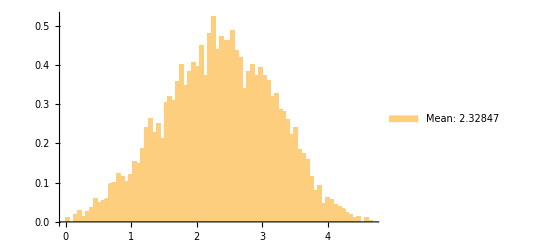
-Graphics-i.i.d Complex Gaussian Channel

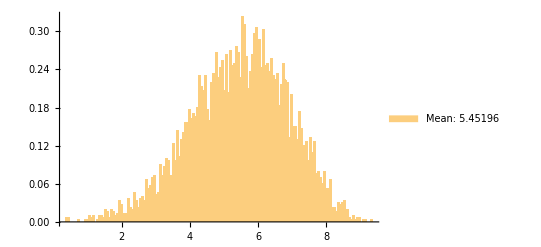
-Graphics-Chaotic Channel

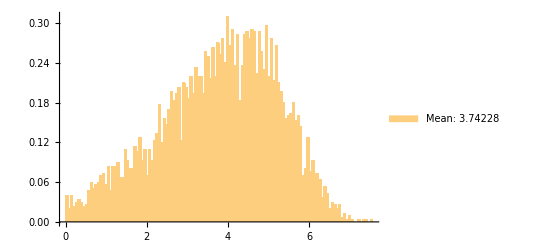
-Graphics-Correlative Channel

```mathematica
CH1Rand:=CH1[[All,singleUser]];
CH2Rand:=CH2[[All,singleUser]];
CH3Rand:=CH3[[All,singleUser]];
rate2CH1:=Log2[1+P*Norm[CH1Rand]^2];
rate2CH2:=Log2[1+P*Norm[CH2Rand]^2];
rate2CH3:=Log2[1+P*Norm[CH3Rand]^2];
Labeled[Histogram[ParallelTable[rate2CH1,{repeat}],{0.06},"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[rate2CH1,{repeat}]//N]]},Bottom]],"i.i.d Complex Gaussian Channel",Top]
Labeled[Histogram[ParallelTable[rate2CH2,{repeat}],{0.06},"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[rate2CH2,{repeat}]//N]]},Bottom]],"Chaotic Channel",Top]
Labeled[Histogram[ParallelTable[rate2CH3,{repeat}],{0.06},"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[rate2CH3,{repeat}]//N]]},Bottom]],"Correlative Channel",Top]
```

2. 	The BS chooses to transmit to a single user with the strongest channel (the user with the highest row norm) and transmits to it at maximum power.

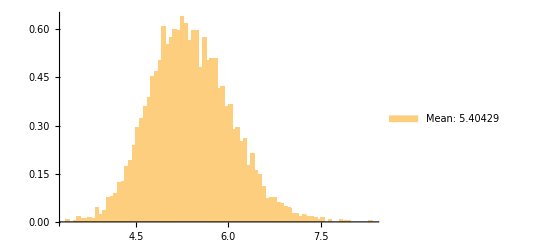
-Graphics-i.i.d Complex Gaussian Channel

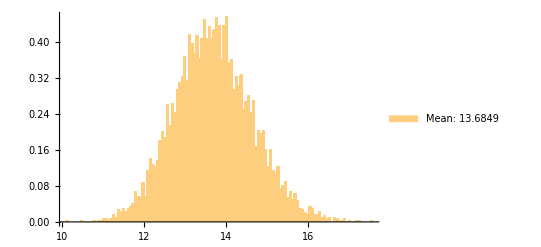
-Graphics-Chaotic Channel

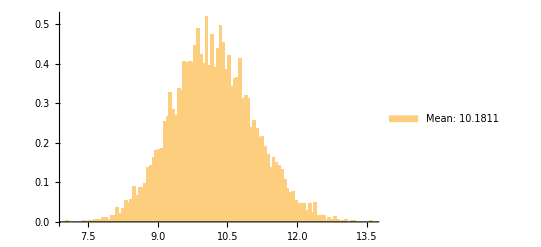
-Graphics-Correlative Channel

```mathematica
rateStrongCH1:=Log2[1+P*Max[Table[Norm[CH1[[All,i]]]^2,{i,k}]]^2];
rateStrongCH2:=Log2[1+P*Max[Table[Norm[CH2[[All,i]]]^2,{i,k}]]^2];
rateStrongCH3:=Log2[1+P*Max[Table[Norm[CH3[[All,i]]]^2,{i,k}]]^2];
Labeled[Histogram[ParallelTable[rateStrongCH1,{repeat}],{0.06},"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[rateStrongCH1,{repeat}]//N]]},Bottom]],"i.i.d Complex Gaussian Channel",Top]
Labeled[Histogram[ParallelTable[rateStrongCH2,{repeat}],{0.06},"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[rateStrongCH2,{repeat}]//N]]},Bottom]],"Chaotic Channel",Top]
Labeled[Histogram[ParallelTable[rateStrongCH3,{repeat}],{0.06},"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[rateStrongCH3,{repeat}]//N]]},Bottom]],"Correlative Channel",Top]
```

3. 	The BS chooses to transmit to 𝑡 randomly chosen users using ZFBF with uniform power allocation between the selected users .

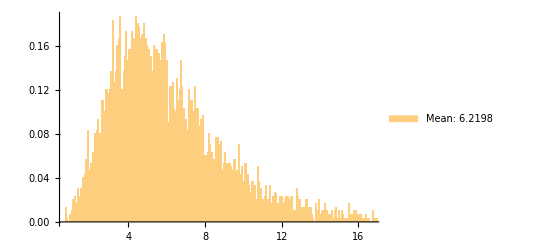
-Graphics-i.i.d Complex Gaussian Channel

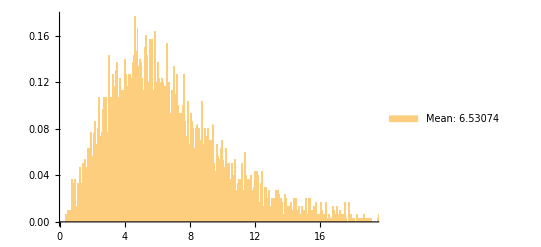
-Graphics-Chaotic Channel

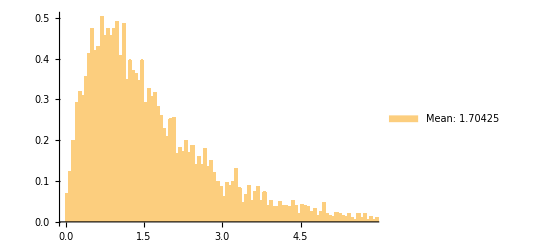
-Graphics-Correlative Channel

```mathematica
Puniformal = P/t// N;
multiUsers = RandomSample[users,t];
CH1Trand:=Table[CH1[[All,multiUsers[[i]]]],{i,t}];
CH2Trand:=Table[CH2[[All,multiUsers[[i]]]],{i,t}];
CH3Trand:=Table[CH3[[All,multiUsers[[i]]]],{i,t}];
ratetRand1:=rateFunc[Puniformal,CH1Trand,Vec[CH1Trand], t];
ratetRand2:=rateFunc[Puniformal,CH2Trand,Vec[CH2Trand], t];
ratetRand3:=rateFunc[Puniformal,CH3Trand,Vec[CH3Trand], t];
(*Output grahp*)
Labeled[Histogram[ParallelTable[ratetRand1,{repeat}],{0.06},"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[ratetRand1,{repeat}]//N]]},Bottom]],"i.i.d Complex Gaussian Channel",Top]
Labeled[Histogram[ParallelTable[ratetRand2,{repeat}],{0.06},"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[ratetRand2,{repeat}]//N]]},Bottom]],"Chaotic Channel",Top]
Labeled[Histogram[ParallelTable[ratetRand3,{repeat}],{0.06},"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[ratetRand3,{repeat}]//N]]},Bottom]],"Correlative Channel",Top]
```

4.  The base station chooses to transmit to the t strongest users using ZFBF, so that the power is equally distributed between the selected users .

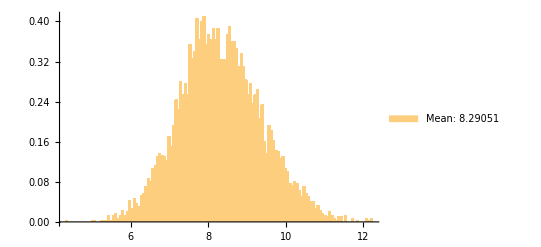
-Graphics-i.i.d Complex Gaussian Channel

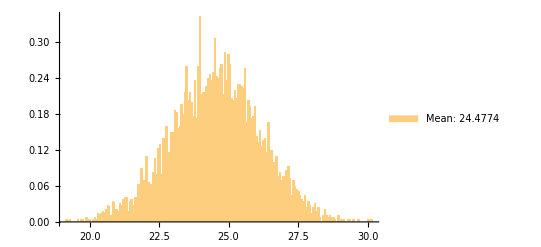
-Graphics-Chaotic Channel

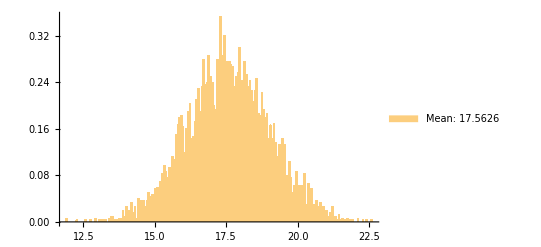
-Graphics-Correlative Channel

```mathematica
ratetStrongestCH1:=rateStrongFunc[Puniformal,StrongestNorm[t,CH1],t];
ratetStrongestCH2:=rateStrongFunc[Puniformal,StrongestNorm[t,CH2],t];
ratetStrongestCH3:=rateStrongFunc[Puniformal,StrongestNorm[t,CH3],t];
Labeled[Histogram[ParallelTable[ratetStrongestCH1,{repeat}],{0.06},"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[ratetStrongestCH1,{repeat}]//N]]},Bottom]],"i.i.d Complex Gaussian Channel",Top]
Labeled[Histogram[ParallelTable[ratetStrongestCH2,{repeat}],{0.06},"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[ratetStrongestCH2,{repeat}]//N]]},Bottom]],"Chaotic Channel",Top]
Labeled[Histogram[ParallelTable[ratetStrongestCH3,{repeat}],{0.06},"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[ratetStrongestCH3,{repeat}]//N]]},Bottom]],"Correlative Channel",Top]
```

5. The BS tests all user subgroups of the size 𝑡, and transmits to the optimal group (e.g., with the highest rates) using ZFBF. The power allocation is uniform between the selected users.

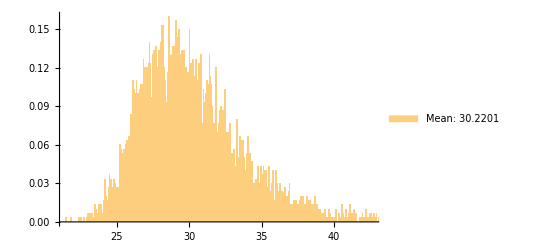
-Graphics-i.i.d Complex Gaussian Channel

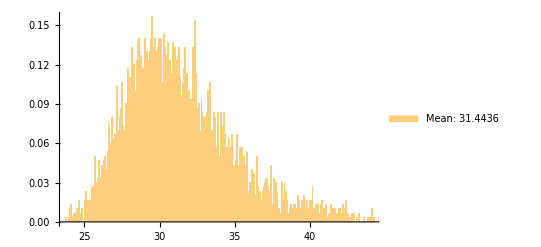
-Graphics-Chaotic Channel

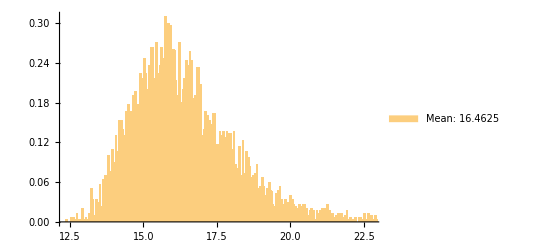
-Graphics-Correlative Channel

```mathematica
t = 2;
SubGroupst =Subsets[users, {t}];
L=Length[SubGroupst];
ListNumGroup = Table[i,{i,L}];
(*Using the function from qustion 3*)
OptimalGroupRateCH1:=Max[Table[rateFunc[Puniformal,CH1,Vec[SubgroupCh[t,L,CH1,SubGroupst][[j]]] , t],{j,L}]];
res1=ParallelTable[OptimalGroupRateCH1,{repeat}];
Labeled[Histogram[res1,{0.06},"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[res1]]},Bottom]],"i.i.d Complex Gaussian Channel",Top]
OptimalGroupRateCH2:=Max[Table[rateFunc[Puniformal,CH2,Vec[SubgroupCh[t,L,CH2,SubGroupst][[j]]] , t],{j,L}]];
res2=ParallelTable[OptimalGroupRateCH2,{repeat}];
Labeled[Histogram[res2,{0.06},"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[res2]]},Bottom]],"Chaotic Channel",Top]
OptimalGroupRateCH3:=Max[Table[rateFunc[Puniformal,CH3,Vec[SubgroupCh[t,L,CH3,SubGroupst][[j]]] , t],{j,L}]];
res3=ParallelTable[OptimalGroupRateCH3,{repeat}];
Labeled[Histogram[res3,{0.06},"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[res3]]},Bottom]],"Correlative Channel",Top]
```